BIOL 214H Presentation Handout

Using SIR Modeling to Understand Pathogens and Population Dynamics

If you would like to follow along and play with the models, click the ‘Make Your Own Copy’ button once opening the link!

## BookChapterNumber.Section. SIR (Susceptible-Infected-Recovered) Model as a System of Nonlinear Equations

Consider the foundational SIR model, presented in Equations 1.1 - 1.3. Note that individuals may not be reinfected (i.e. once recovered, always recovered) and that this model includes only one viral strain with no vaccination or death components.

S_(t+1)=S_t-f S_t I_t

I_(t+1)=I_t+ f S_t I_t - r I_t

R_(t+1)=R_t+r I_t;

### BookChapterNumber.Section.Subsection. Model Assumptions, Requirements, and Parameters

An important feature of the model presented above is that, for all times t, S_(t+1)+I_(t+1)+R_(t+1)=S_t+I_t+R_t; that is, no individuals enter or leave the population. Additionally, and this is important for parameterization of the model, is that S_t, I_t, R_t > 0 at all times t. Certain values of f and/or r could mechanically cause counts of each subclass of the population to go negative, and so for the first requirement to hold, specifying  f << 1, for example, is good practice to prevent such from occurring while still allowing for the model to meaningfully characterize these dynamics. Lastly, as mentioned before, permanent immunity is granted to any individual who has been infected and recovered from the virus.

Table BookChapterNumber.TableTitle.   SIR Model Variables and Parameters

Symbol | Definition
S_t,I_t,R_t | Susceptible, Infected, and Recovered individuals, respectfully, at time t
f    | (Scaled) proportion of susceptible individuals that become infected
r | (Scaled) proportion of infected individuals that recover

### BookChapterNumber.Section.Subsection. Mathematica Code

The below cell of Mathematica code contains a module that runs this system of equations whose parameters can be easily changed to realize hypothetical scenarios (see the call to the module below its definition).

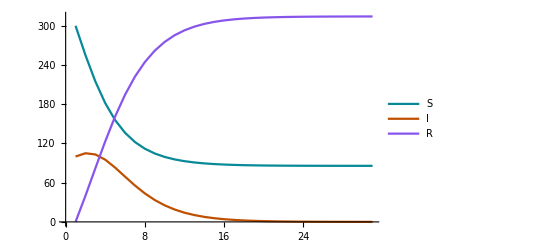

```mathematica
(* Define the module *)
BaseSIR[St0_,It0_,Rt0_,f_,r_,niter_]:=(
Subscript[S, t]=St0; (* Set initial susceptible, infected, and recovered *)
Subscript[I, t]=It0;
Subscript[R, t]=Rt0;
results = Table[0,{i,niter + 1},{j,3}]; (* Create array for storing iterations, include initial values *)
results[[1]][[1;;3]]={Subscript[S, t],Subscript[I, t],Subscript[R, t]};
For[i=1,i<=niter,i++,
	(* Perform iteration *)
	Subscript[S, t+1]= Subscript[S, t]-f Subscript[S, t] Subscript[I, t];
	Subscript[I, t+1]=Subscript[I, t]+f Subscript[S, t] Subscript[I, t] - Subscript[I, t] r;
	Subscript[R, t+1]=Subscript[R, t]+Subscript[I, t] r;
	
	(* Update values *)
	Subscript[S, t]=Subscript[S, t+1];
	Subscript[I, t]=Subscript[I, t+1];
	Subscript[R, t]=Subscript[R, t+1];
	results[[i+1]][[1;;3]]={Subscript[S, t+1],Subscript[I, t+1],Subscript[R, t+1]}; (* Store values *)
];
ListPlot[Transpose[results],Joined->True, PlotLegends->{"S","I","R"}] (* Return plot of array *)
);
example1 = BaseSIR[300,100,0,0.0015,0.4,30] (* Call module *)
```

## BookChapterNumber.Section. SIR Model with Reinfection

Consider this modified SIR model, presented in Equations 1.4 - 1.6. Note that individuals may be reinfected, and that the same assumptions as in Section 1.1 hold.

S_(t+1)=S_t-f S_t I_t+c R_t

I_(t+1)=I_t+ f S_t I_t - r I_t

R_(t+1)=R_t+r I_t-c R_t;

### BookChapterNumber.Section.Subsection. Model Assumptions, Requirements, and Parameters

The model in Equations 1.4 - 1.6 is defined as in Table 1.1, with the noted addition of c representing the proportion of recovered individuals who lose their immunity after each iteration.

### BookChapterNumber.Section.Subsection. Mathematica Code

Below is the updated Mathematica Code to account for the chance of reinfection.

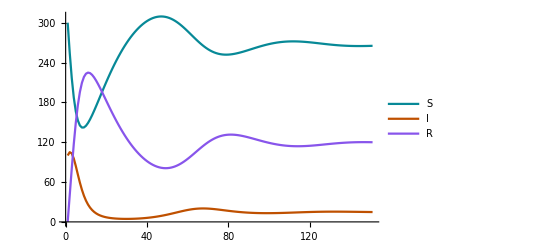

```mathematica
(* Define the module *)
ModifiedSIR[St0_,It0_,Rt0_,f_,r_,s_,niter_]:=(
Subscript[S, t]=St0; (* Set initial susceptible, infected, and recovered *)
Subscript[I, t]=It0;
Subscript[R, t]=Rt0;
results = Table[0,{i,niter + 1},{j,3}]; (* Create array for storing iterations, include initial values *)
results[[1]][[1;;3]]={Subscript[S, t],Subscript[I, t],Subscript[R, t]};
For[i=1,i<=niter,i++,
	(* Perform iteration *)
	Subscript[S, t+1]= Subscript[S, t]-f Subscript[S, t] Subscript[I, t]+s Subscript[R, t];
	Subscript[I, t+1]=Subscript[I, t]+f Subscript[S, t] Subscript[I, t] - Subscript[I, t] r;
	Subscript[R, t+1]=Subscript[R, t]+Subscript[I, t] r-s Subscript[R, t];
	
	(* Update values *)
	Subscript[S, t]=Subscript[S, t+1];
	Subscript[I, t]=Subscript[I, t+1];
	Subscript[R, t]=Subscript[R, t+1];
	results[[i+1]][[1;;3]]={Subscript[S, t+1],Subscript[I, t+1],Subscript[R, t+1]}; (* Store values *)
];
ListPlot[Transpose[results],Joined->True, PlotLegends->{"S","I","R"}] (* Return plot of array *)
);
example1 = ModifiedSIR[300,100,0,0.0015,0.4,0.05,150] (* Call module *)
```

## BookChapterNumber.Section. Including Vaccinations

With vaccinations, two principal concerns about their role in stopping viral transmissions is quantity and efficacy.

### BookChapterNumber.Section.Subsectiona. Tracking Quantity of Vaccinations over Time

Slightly modifying Equations 1.1 - 1.3, we have the following SIRV (Susceptible-Infected-Recovered-Vaccinated) Model. Note the addition of a new parameter, b, representing the proportion of additional susceptible individuals vaccinated in each iteration. Individuals who were infected or recovered at a time t were assumed to not become vaccinated, as an infected person could transmit the virus to an individual administering a vaccine, and a recovered person need not receive a vaccine, should they be immune. By definition, b < 1.

S_(t+1)=S_t-f S_t I_t - b S_t

I_(t+1)=I_t+ f S_t I_t - r I_t

R_(t+1)=R_t+r I_t

V_(t+1)=V_t+b S_t

Again, permanent immunity is given to individuals who are recovered/vaccinated from the virus. The aforementioned assumption regarding the population totals remaining constant throughout time also holds in this case.

Table BookChapterNumber.TableTitle.   SIRV Model Variables and Parameters

With the addition of b, as defined above, and V_t, the number of vaccinated persons at time t, see Table 1.1 for additional parameters and variable definitions.

### BookChapterNumber.Section.1b. Mathematica Code

Below is a Mathematica implementation of this SIRV model.

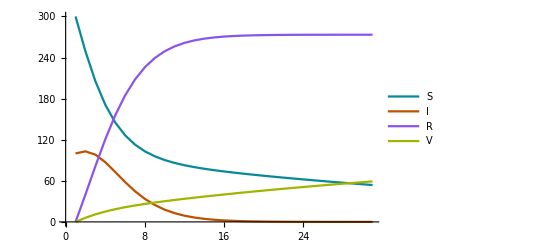

```mathematica
(* Define the module *)
BaseSIRV[St0_,It0_,Rt0_,Vt0_,f_,r_,b_,niter_]:=(
Subscript[S, t]=St0; (* Set initial susceptible, infected, and recovered *)
Subscript[I, t]=It0;
Subscript[R, t]=Rt0;
Subscript[V, t]=Vt0;
results = Table[0,{i,niter + 1},{j,4}]; (* Create array for storing iterations, include initial values *)
results[[1]][[1;;4]]={Subscript[S, t],Subscript[I, t],Subscript[R, t],Subscript[V, t]};
For[i=1,i<=niter,i++,
	(* Perform iteration *)
	Subscript[S, t+1]= Subscript[S, t]-f Subscript[S, t] Subscript[I, t]-b Subscript[S, t];
	Subscript[I, t+1]=Subscript[I, t]+f Subscript[S, t] Subscript[I, t] - r Subscript[I, t] - b Subscript[I, t];
	Subscript[R, t+1]=Subscript[R, t]+ r Subscript[I, t];
	Subscript[V, t+1]=Subscript[V, t]+ b Subscript[S, t];
	
	(* Update values *)
	Subscript[S, t]=Subscript[S, t+1];
	Subscript[I, t]=Subscript[I, t+1];
	Subscript[R, t]=Subscript[R, t+1];
	Subscript[V, t]=Subscript[V, t+1];
	results[[i+1]][[1;;4]]={Subscript[S, t+1],Subscript[I, t+1],Subscript[R, t+1],Subscript[V, t+1]}; (* Store values *)
];
ListPlot[Transpose[results],Joined->True, PlotLegends->{"S","I","R","V"}] (* Return plot of array *)
)
example2 = BaseSIRV[300,100,0,0,0.0015,0.4,0.02,30](* Call module *)
```

### BookChapterNumber.Section.2a. Incorporating Efficacy of Vaccines

Conceptually, there is no “right way or the highway” approach to modeling the efficacy, or potential to prevent reinfection or serious symptoms of/from a virus, of vaccines. If a virus undergoes a sudden mutation, vaccine efficacy could take a sudden drop. If permanent immunity is granted to vaccinated individuals, then there is no decrease in the preventative qualities of a vaccine. With that in mind, modeling the efficacy of a vaccine should take much the same approach. Hence, Equations 1.8 - 1.11 present an arguably generalized method to model such, but implementations should clear up any confusion.

S_(t+1)=S_t-f S_t I_t - b S_t+k(1-v(t))V_t

I_(t+1)=I_t+ f S_t I_t - r I_t +w(1-v(t))V_t

R_(t+1)=R_t+r I_t

V_(t+1)=V_t+b S_t -(1-v(t))V_t

The obvious question: what is v(t)? In short, the function is defined mathematically as

v(t): ℝ_+-> [0,1]

such that, for increasing t, the returned value may decrease (i.e. efficacy of a vaccine decreases with time), stay the same, or any other desired behavior. Because the function has range [0,1], it can be thought of as a proportion of vaccinated individuals that become susceptible, thus allowing for the possibility of reinfection. In Section 1.3.2b, three potential v(t) are presented: the Sigmoid function (very close in appearance to the logistic growth curve), a constant-valued function (for no loss in efficacy), or a linear decay function (for initially more rapid loss in efficacy than the Sigmoid function).

Additionally, note k and w -- these represent, respectively, the proportion of vaccinated individuals who become Susceptible or (Re)-Infected! In order to satisfy the model assumptions, however, k + w = 1.

Note that the variables and parameters of Table 1.1 and Section 1.2.1a carry over to this extension of the normal SIRV model, with the additional v(t) function.

### BookChapterNumber.Section.2b. Mathematica Code

The code below represents implementation of this modified SIRV model with potential different v(t), each representing different scenarios of vaccine efficacy.

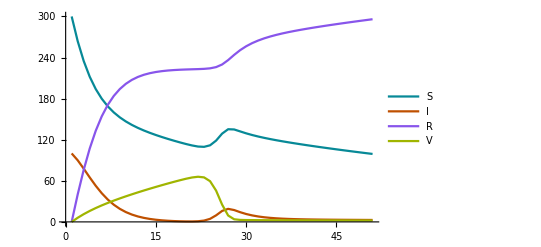

```mathematica
CustomVaccineFunction[type_,t_,decayTerm_,const_]:=(
If[type==1,
	Return[1 - (1 / (1 + Exp[-(t-decayTerm)]))], (* Transformation of the Sigmoid Function: Slow, logistic decay *)
	If[type==2,
		Return[const], (* Constant efficacy at any time t *)
		If[type==3,
			Return[1-(t/niter)] (* Linear decay of efficacy with time t *)
			]
		]
	]
);

ModifiedSIRV[St0_,It0_,Rt0_,Vt0_,f_,r_,b_,k_,w_,type_,decayTerm_,const_,niter_]:=(
Subscript[S, t]=St0; (* Set initial susceptible, infected, and recovered *)
Subscript[I, t]=It0;
Subscript[R, t]=Rt0;
Subscript[V, t]=Vt0;
results = Table[0,{i,niter + 1},{j,4}]; (* Create array for storing iterations, include initial values *)
results[[1]][[1;;4]]={Subscript[S, t],Subscript[I, t],Subscript[R, t],Subscript[V, t]};
For[i=1,i<=niter,i++,
	(* Perform iteration *)
	Subscript[S, t+1]= Subscript[S, t]-f Subscript[S, t] Subscript[I, t]-b Subscript[S, t] + k(1-CustomVaccineFunction[type,i,decayTerm,const])Subscript[V, t];
	Subscript[I, t+1]=Subscript[I, t]+f Subscript[S, t] Subscript[I, t] -r Subscript[I, t]+w(1-CustomVaccineFunction[type,i,decayTerm,const])Subscript[V, t];
	Subscript[R, t+1]=Subscript[R, t]+r Subscript[I, t];
	Subscript[V, t+1]=Subscript[V, t]+b Subscript[S, t]-(1-CustomVaccineFunction[type,i,decayTerm,const])Subscript[V, t];
	
	(* Update values *)
	Subscript[S, t]=Subscript[S, t+1];
	Subscript[I, t]=Subscript[I, t+1];
	Subscript[R, t]=Subscript[R, t+1];
	Subscript[V, t]=Subscript[V, t+1];
	results[[i+1]][[1;;4]]={Subscript[S, t+1],Subscript[I, t+1],Subscript[R, t+1],Subscript[V, t+1]} (* Store values *)
];
ListPlot[Transpose[results],Joined->True, PlotLegends->{"S","I","R","V"}] (* Return plot of array *) 
)

example1 = ModifiedSIRV[300,100,0,0,0.001,0.4,0.02,0.6,0.4,1,25,1/30,50](* Call module *)
```

## BookChapterNumber.Section. Multiple Strains and Co-infection

As the COVID-19 pandemic has lasted for more than two years, viruses such as influenza have sparked concern over the possibility of an individual becoming infected with one or both of the viruses. Whether or not there is any relationship between becoming infected with COVID-19 and the change in risk of exposure to influenza, and vice versa, is a more intensive biological question, but the general question still remains: how do multiple viruses infecting a population at the same time interact with one another, if at all?

### BookChapterNumber.Section.Subsectiona. Multiple Strains with No Co-infection

The following model assumes rather important information, and so prior to its presentation, let’s understand the behind-the-scenes of this modified SIRV model:

1. The multiple strains are of a shared or closely-related pathogen, such that a single vaccination is intended to provide protection against both.

2. Permanent immunity is granted to any recovered or vaccinated individual. (Adapting this model with one such as in Section 1.2.2b is possible, however.)

And, as before, no individual leaves or enters the population.

Therefore, we have the system of equations given below:

S_(t+1)=S_t-f_1 S_t I_(1,t) -f_2 S_t I_(2,t)- b S_t

I_(1,t+1)=I_(1,t)+ f_1 S_t I_(1,t) - r_1 I_(2,t)

I_(2,t+1)=I_(2,t)+ f_2 S_t I_(2,t) - r_1 I_(1,t)

R_(t+1)=R_t+r_1 I_(1,t) +r_2 I_(2,t)

V_(t+1)=V_t+b S_t

Note that f_1,f_2,r_1, and r_2 fulfill the same roles as in the SIR model first presented, but for Strain 1 and 2, accordingly.

### BookChapterNumber.Section.1b. Mathematica Code

Consider the following code for this model. Note how, in this example, one virus is clearly more infectious as the other, though both exhibit similar behavior throughout the simulation.

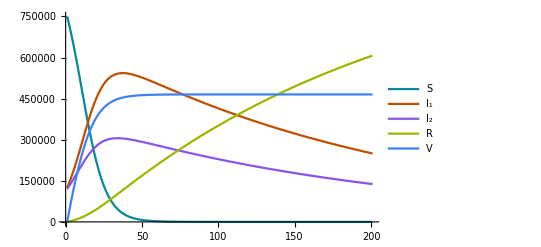

```mathematica
MultiStrainSIRV[St0_,I1t0_,I2t0_,Rt0_,Vt0_,f1_,f2_, r1_, r2_,b_,niter_]:=(
Subscript[S, t]=St0; (* Set initial susceptible, infected, and recovered *)
Subscript[I, 1,t]=I1t0;
Subscript[I, 2,t]=I2t0;
Subscript[R, t]=Rt0;
Subscript[V, t]=Vt0;
results = Table[0,{i,niter + 1},{j,5}]; (* Create array for storing iterations, include initial values *)
results[[1]][[1;;5]]={Subscript[S, t],Subscript[I, 1,t],Subscript[I, 2,t],Subscript[R, t],Subscript[V, t]};
For[i=1,i<=niter,i++,
	(* Perform iteration *)
	Subscript[S, t+1]= Subscript[S, t]-Subscript[S, t](f1 Subscript[I, 1,t]+f2 Subscript[I, 2,t]);
	Subscript[I, 1,t+1]=Subscript[I, 1,t]+f1 Subscript[S, t] Subscript[I, 1,t] - Subscript[I, 1,t] r1;
	Subscript[I, 2,t+1]=Subscript[I, 2,t]+f2  Subscript[S, t] Subscript[I, 2,t] - Subscript[I, 2,t] r2;
	Subscript[R, t+1]=Subscript[R, t]+Subscript[I, 1,t] r1+Subscript[I, 2,t] r2;
	Subscript[V, t+1]= Subscript[V, t]+b Subscript[S, t];
	
	(* Update values *)
	        Subscript[S, t]=Subscript[S, t+1];
	Subscript[I, 1,t]=Subscript[I, 1,t+1];
	Subscript[I, 2,t]=Subscript[I, 2,t+1];
	Subscript[R, t]=Subscript[R, t+1];
	Subscript[V, t]=Subscript[V, t+1];
	results[[i+1]][[1;;5]]={Subscript[S, t+1],Subscript[I, 1,t+1],Subscript[I, 2,t+1],Subscript[R, t+1],Subscript[V, t+1]} (* Store values *)
];
ListPlot[Transpose[results],Joined->True, PlotLegends->{"S","I_1","I_2","R","V"}] (* Return plot of array *)
)
example1 = MultiStrainSIRV[750000,125000,120000,0,0,1.5*10^-7,1*10^-7,0.005,0.005,0.04,200](* Call module *)
```

### BookChapterNumber.Section.2a. Multiple Strains with Co-infection

In modeling co-infection, in which an individual exhibits symptoms emblematic of becoming infected with multiple strains of a virus (if such were biologically possible), or potentially two different viruses altogether, we derived the following system of equations.

It is worth noting the below Mathematica simulation, in which infections far outpace recovery under these parameters; this is a viable representation of the phenomenon that is co-infection, considering the likely difficulty present to recover from simultaneous infections, especially if symptoms are compounded as a result.

With that being said, consider the modification to the SIRV analog presented in Equations 1.12 - 1.16:

S_(t+1)=S_t-f_1 S_t I_(1,t) -f_2 S_t I_(2,t)- f_3 S_t I_(1,t)I_(2,t)- b S_t

I_(1,t+1)=I_(1,t)+ f_1 S_t I_(1,t) - r_1 I_(2,t)

I_(2,t+1)=I_(2,t)+ f_2 S_t I_(2,t) - r_1 I_(1,t)

C_(t+1)=C_t+f_3 S_t I_(1,t)I_(2,t)-r_3 C_t

R_(t+1)=R_t+r_1 I_(1,t) +r_2 I_(2,t) +r_3 C_t

V_(t+1)=V_t+b S_t

At this point, the system of equations is... large. Complicated. (You may be thinking it’s absurd.) This section is both an attempt to model a biological rarity, but a possibility, and to highlight how finicky SIR models can be -- small changes in parameters can yield drastic, and often times unrealistic, changes in results.

As a result of this, look at Section 2! It highlights a stochastic mechanism known as Monte Carlo Simulations, by which population dynamics such as these may be approached more mechanically.

### BookChapterNumber.Section.2b. Mathematica Code

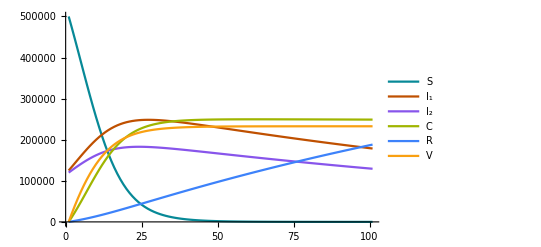

```mathematica
(* Define the module *)
MultiStrainCoInfSIRV[St0_,I1t0_,I2t0_,Rt0_,Vt0_,f1_,f2_,f3_, r1_, r2_,r3_,b_,niter_]:=(
Subscript[S, t]=St0; (* Set initial values *)
Subscript[I, 1,t]=I1t0;
Subscript[I, 2,t]=I2t0;
Subscript[C, t]=0;
Subscript[R, t]=Rt0;
Subscript[V, t]=Vt0;
results = Table[0,{i,niter + 1},{j,6}]; (* Create array for storing iterations, include initial values *)
results[[1]][[1;;6]]={Subscript[S, t],Subscript[I, 1,t],Subscript[I, 2,t],Subscript[C, t],Subscript[R, t],Subscript[V, t]};
For[i=1,i<=niter,i++,
	(* Perform iteration *)
	Subscript[S, t+1]= Subscript[S, t]-Subscript[S, t](f1 Subscript[I, 1,t]+f2 Subscript[I, 2,t])-f3 Subscript[S, t] Subscript[I, 1,t] Subscript[I, 2,t];
	Subscript[I, 1,t+1]=Subscript[I, 1,t]+f1 Subscript[S, t] Subscript[I, 1,t] -r1 Subscript[I, 1,t];
	Subscript[I, 2,t+1]=Subscript[I, 2,t]+f2  Subscript[S, t] Subscript[I, 2,t] -r2 Subscript[I, 2,t];
	Subscript[C, t+1]=Subscript[C, t]+f3 Subscript[S, t] Subscript[I, 1,t] Subscript[I, 2,t]-r3 Subscript[C, t];
	Subscript[R, t+1]=Subscript[R, t]+r1 Subscript[I, 1,t]+r2 Subscript[I, 2,t]+r3 Subscript[C, t];
	Subscript[V, t+1]= Subscript[V, t]+b Subscript[S, t];
	
	(* Update values *)
	Subscript[S, t]=Subscript[S, t+1];
	Subscript[I, 1,t]=Subscript[I, 1,t+1];
	Subscript[I, 2,t]=Subscript[I, 2,t+1];
	Subscript[C, t]=Subscript[C, t+1];
	Subscript[R, t]=Subscript[R, t+1];
	Subscript[V, t]=Subscript[V, t+1];
	results[[i+1]][[1;;6]]={Subscript[S, t+1],Subscript[I, 1,t+1],Subscript[I, 2,t+1],Subscript[C, t+1],Subscript[R, t+1],Subscript[V, t+1]} (* Store values *)
];
ListPlot[Transpose[results],Joined->True, PlotLegends->{"S","I_1","I_2","C","R","V"}] (* Return plot of array *)
)
example1 = MultiStrainCoInfSIRV[500000,125000,120000,0,0,1.5*10^-7,1*10^-7,1.5*10^-12,0.005,0.005,0.0001,0.04,100](* Call module *)
```

Monte-Carlo Simulations: Incorporating Space into Population Dynamics

Before diving into a rather large algorithm, let’s first define a Monte-Carlo simulation and understand its usefulness.

In short, a Monte-Carlo simulation is a process that takes advantage of stochasticity and random variables to perform multiple, independent runs of the same algorithm. The multiple runs are then averaged to obtain an empirical estimate of the population dynamics under a set of parameters.

Why Monte-Carlo? As long as the algorithm sticks to its biological assumptions, we can be much more mechanical in how we approach the problem at-hand. Although, the time taken to run such an algorithm is a notable drawback.

For the different Monte-Carlo simulations presented below, the general framework is as follows:

1. Place N individuals uniformly at random on a grid, or “habitat.”

2. According to initial-value parameters, mark appropriate totals of individuals as Susceptible, Infected, etc.

3. For each iteration,

3a. Determine if the individual moves via a Bernoulli random variable (a.k.a. a coin flip).

3b. If 3a, move the individual a random amount in each direction, sampled from a N(0,1) distribution (i.e. a standard normal distribution).

3c. Obtain a distance matrix that represents the Euclidean distance between each pair of individuals.

4.  For each pair of individuals, if they are within some distance threshold, determine, subject to necessary constraints, if an infection occurs.

5. Count up the number of individuals belonging to each class of the model.

## 2.1. SIR Model as a Monte-Carlo Simulation

Note: If you are viewing this online, you may have to download the notebook to run these, as the cells are apparently too large in length!

### 2.1.1. Simulation Parameters and Variables

The code below presents an implementation of the above algorithm, where individuals belong to any one of the three classes of an SIR model. See Table 2.1 for the parameters of interest.

Table BookChapterNumber.TableTitle.   SIR Model Variables and Parameters

Symbol | Definition | Symbol | Definition
N | Total population (S_t+I_t+R_t) | permImmunity | Do recovered individuals have permanent immunity?
S_t | Number of Susceptible Individuals (St0 := Initial amount) | reinf | If no permanent immunity, coefficient of a distribution parameter (larger = more likely for reinfection).
I_t | Number of Infected Individuals (It0 := Initial amount) | recovThresh | Threshold for a sampled Poisson distribution for recovery
R_t | Number of Recovered Individuals (Rt0 := Initial amount) | recov | Parameter to Poisson distribution for recovery
infThresh | Distance threshold for an infection to occur | niter | Number of iterations in one run of a Monte-Carlo algorithm
inf | Cutoff for a sampled value from a Poisson distribution for infection | nruns | Number of runs of a Monte-Carlo algorithm

### 2.1.2. Mathematica Code

```mathematica
SimulateSIR[N_, St0_, It0_, Rt0_, infThresh_, inf_, permImmunity_, reinf_, recovThresh_, recov_, niter_, makeMovie_] := (
  results = Table[0, {i, niter + 1}, {j, 3}];
  movie = ConstantArray[0, niter + 1];
  results[[1]][[1 ;; 3]] = {St0, It0, Rt0};
  (* Step 1: Create the N individuals, according to initial classifications *)
  x = RandomVariate[UniformDistribution[{-3.5, 3.5}], N];
  y = RandomVariate[UniformDistribution[{-3.5, 3.5}], N];
  idvs = Table[0, {i, N}];
  For[i = 1, i <= St0, i++,
   	idvs[[i]] = {x[[i]], y[[i]], "S"};
   ];
  For[i = St0 + 1, i <= St0 + It0, i++,
   	idvs[[i]] = {x[[i]], y[[i]], "I"};
   ];
  For[i = St0 + It0 + 1, i <= St0 + It0 + Rt0, i++,
   	idvs[[i]] = {x[[i]], y[[i]], "R"};
   ];
  
  (* Step 1b: If Making a Movie, Set the Initial Frame *)
  If[makeMovie,
   plotData = {};
   plotLegend = {};
   
   susc = {};
   infec = {};
   reco = {};
   For[i = 1, i <= Length[idvs], i++,
    If[idvs[[i]][[3]] == "S", AppendTo[susc, idvs[[i]][[1 ;; 2]]]];
    If[idvs[[i]][[3]] == "I", AppendTo[infec, idvs[[i]][[1 ;; 2]]]];
    If[idvs[[i]][[3]] == "R", AppendTo[reco, idvs[[i]][[1 ;; 2]]]];
    ];
   
   If[Length[susc] > 0,
    AppendTo[plotData, susc];
    AppendTo[plotLegend, StringJoin["Susceptible: ", ToString[St0]]];
    ];
   If[Length[infec] > 0,
    AppendTo[plotData, infec];
    AppendTo[plotLegend, StringJoin["Infected: ", ToString[It0]]];
    ];
   If[Length[reco] > 0,
    AppendTo[plotData, reco];
    AppendTo[plotLegend, StringJoin["Recovered: ", ToString[Rt0]]];
    ];
   
   movie[[1]] = Show[ListPlot[plotData, PlotLegends -> plotLegend, PlotRange -> {{-6, 6}, {-6, 6}}]];
   ];
  
  For[n = 2, n <= niter + 1, n++,
   (* Step 2: Determine if They Move *)
   move = {};
   For[i = 1, i <= Length[idvs], i++,
    	AppendTo[move, RandomVariate[BernoulliDistribution[0.5]]];
    ];
   
   (* Step 3: Move the Individuals *)
   For[i = 1, i <= Length[idvs], i++,
    If[move[[i]] == 1,
     x = RandomVariate[NormalDistribution[0, 1], 1][[1]];
     y = RandomVariate[NormalDistribution[0, 1], 1][[1]];
     idvs[[i]][[1]] = idvs[[i]][[1]] + x;
     idvs[[i]][[2]] = idvs[[i]][[2]] + y;
     ]
    ];
   
   (* Step 4a: Get Distances Between Each Pair of Individuals *)
   coords = Table[0, {i, N}, {j, 2}];
   For[i = 1, i <= Length[idvs], i++,
    coords[[i]][[1 ;; 2]] = idvs[[i]][[1 ;; 2]];
    ];
   distances = DistanceMatrix[coords];
   Clear[coords];
   
   (* Step 4b: Infect Individuals Subject to All Constraints *)
   For[i = 1, i <= Length[idvs], i++,
    For[j = i + 1, j <= Length[idvs], j++,
     If[(idvs[[i]][[3]] == "I" || idvs[[j]][[3]] == "I") && distances[[i]][[j]] < infThresh,
      lambda = Abs[infThresh - distances[[i]][[j]]];
      
      infect = RandomVariate[PoissonDistribution[lambda], 1][[1]];
      
      If[permImmunity,
       infect = 0,
       If[idvs[[i]][[3]] == "R" || idvs[[j]][[3]] == "R",
        lambda = lambda * reinf;
        infect = RandomVariate[PoissonDistribution[lambda], 1][[1]];
        ]
       ];
      
      If[infect > inf,
       idvs[[i]][[3]] = "I";
       idvs[[j]][[3]] = "I";
       
       ]
      ]
     ]
    ];
   
   (* Step 5: Mark Recovered Individuals, Mark Newly Susceptible Individuals, Count Individuals *)
   nS = 0;
   nI = 0;
   nR = 0;
   
   For[k = 1, k <= Length[idvs], k++,
    If[idvs[[k]][[3]] == "I" && (RandomVariate[PoissonDistribution[recov], 1][[1]] >= recovThresh), idvs[[k]][[3]] = "R"];
    
    If[idvs[[k]][[3]] == "S", nS = nS + 1, If[idvs[[k]][[3]] == "I", nI = nI + 1, nR = nR + 1]];
    ];
   results[[n]][[1 ;; 3]] = {nS, nI, nR};
   
   If[makeMovie,
    plotData = {};
    plotLegend = {};
    
    susc = {};
    infec = {};
    reco = {};
    For[i = 1, i <= Length[idvs], i++,
     If[idvs[[i]][[3]] == "S", AppendTo[susc, idvs[[i]][[1 ;; 2]]]];
     If[idvs[[i]][[3]] == "I", AppendTo[infec, idvs[[i]][[1 ;; 2]]]];
     If[idvs[[i]][[3]] == "R", AppendTo[reco, idvs[[i]][[1 ;; 2]]]];
     ];
    
    If[Length[susc] > 0,
     AppendTo[plotData, susc];
     AppendTo[plotLegend, StringJoin["Susceptible: ", ToString[nS]]];
     ];
    If[Length[infec] > 0,
     AppendTo[plotData, infec];
     AppendTo[plotLegend, StringJoin["Infected: ", ToString[nI]]];
     ];
    If[Length[reco] > 0,
     AppendTo[plotData, reco];
     AppendTo[plotLegend, StringJoin["Recovered: ", ToString[nR]]];
     ];
    
    movie[[n]] = Show[ListPlot[plotData, PlotLegends -> plotLegend, PlotRange -> {{-6, 6}, {-6, 6}}]];
    ];
   
   ];
  If[makeMovie, Return[movie], Return[results]];
  )

MonteCarloBasicSIR[N_, St0_, It0_, Rt0_, thresh_, inf_, permImmunity_, reinf_, recovThresh_, recov_, niter_, nruns_] := (
  avgResults = Table[0, {i, niter + 1}, {j, 3}];
  Do[
   sim = SimulateSIR[N, St0, It0, Rt0, thresh, inf, permImmunity, reinf, recov, recovThresh, niter, False];
   avgResults = avgResults + (1/nruns)*sim;
   , {r, nruns}];
  ListPlot[Transpose[avgResults], Joined -> True, PlotLegends -> {"S", "I", "R"}]
  )

BasicSIRMovie[N_, St0_, It0_, Rt0_, thresh_, inf_, permImmunity_, reinf_, recovThresh_, recov_, niter_] := (
  movie = SimulateSIR[N, St0, It0, Rt0, thresh, inf, permImmunity, reinf, recov, recovThresh, niter, True];
  ListAnimate[movie]
  )
```

```mathematica
(* This... will take a minute or two! *)
MonteCarloBasicSIR[400, 350, 50, 0, 1, 1.5, False, 0.25, 1.5, 3, 30,15];
```

```mathematica
(* Run this for a movie! *)
BasicSIRMovie[400, 350, 50, 0, 1, 1.5, False, 0.25, 1.5, 3, 30];
```

## 2.2. SIRV Model as a Monte-Carlo Simulation

### 2.2.1. Simulation Parameters, Variables, and New Assumptions

Consider the presented simulation in Section 2.1, but now account for vaccinations according to the assumptions below:

1. Any individual may become vaccinated at any time -- formerly, only susceptible people transitioned to a vaccinated state.

2. If permanent immunity is not granted, vaccinated people have a different likelihood of reinfection than do those who have recovered. The efficacy of the vaccine is implied in the reinfV parameter, where a lower value corresponds to a

higher efficacy.

### 2.2.2. Mathematica Code

```mathematica
SimulateSIRV[N_,St0_,It0_,Rt0_,Vt0_,infThresh_,inf_,permImmunity_,reinf_,recovThresh_,recov_,reinfV_,vaccin_,vaccThresh_,niter_,makeMovie_]:= (
results = Table[0,{i,niter + 1},{j,4}];
movie = ConstantArray[0,niter+1];
results[[1]][[1;;4]]={St0,It0,Rt0,Vt0};
(* Step 1: Create the N individuals, according to initial classifications *)
x = RandomVariate[UniformDistribution[{-3,3}],N];
y = RandomVariate[UniformDistribution[{-3,3}],N];
idvs = Table[0,{i,N}];
For[i=1,i<=St0,i++,
	idvs[[i]]= {x[[i]],y[[i]],"S"};
];
For[i=St0+1,i<=St0+It0,i++,
	idvs[[i]]= {x[[i]],y[[i]],"I"};
];
For[i=St0+It0+1,i<=St0+It0+Rt0,i++,
	idvs[[i]]= {x[[i]],y[[i]],"R"};
];
For[i=St0+It0+Rt0+1,i<=St0+It0+Rt0+Vt0,i++,
	idvs[[i]]= {x[[i]],y[[i]],"V"};
];

(* Step 1b: If Making a Movie, Set the Initial Frame *)
If[makeMovie,
plotData ={};
plotLegend={};

susc = {};
infec = {};
reco= {};
vacc ={};
For[i=1,i<=Length[idvs],i++,
If[idvs[[i]][[3]]=="S",AppendTo[susc,idvs[[i]][[1;;2]]]];
If[idvs[[i]][[3]]=="I",AppendTo[infec,idvs[[i]][[1;;2]]]];
If[idvs[[i]][[3]]=="R",AppendTo[reco,idvs[[i]][[1;;2]]]];
If[idvs[[i]][[3]]=="V",AppendTo[vacc,idvs[[i]][[1;;2]]]];
];

If[Length[susc]>0,
AppendTo[plotData,susc];
AppendTo[plotLegend,StringJoin["Susceptible: ", ToString[St0]]];
];
If[Length[infec]>0,
AppendTo[plotData,infec];
AppendTo[plotLegend,StringJoin["Infected: ", ToString[It0]]];
];
If[Length[reco]>0,
AppendTo[plotData,reco];
AppendTo[plotLegend,StringJoin["Recovered: ", ToString[Rt0]]];
];
If[Length[vacc]>0,
AppendTo[plotData,vacc];
AppendTo[plotLegend,StringJoin["Vaccinated: ", ToString[Vt0]]];
];

movie[[1]]=Show[ListPlot[plotData,PlotLegends->plotLegend,PlotRange->{{-6,6},{-6,6}}]];
];

For[n=2,n<=niter+1,n++,
(* Step 2: Determine if They Move *)
move = {};
For[i=1,i<=Length[idvs],i++,
	AppendTo[move,RandomVariate[BernoulliDistribution[0.5]]];
];

(* Step 3: Move the Individuals *)
For[i=1,i<=Length[idvs],i++,
If[move[[i]]==1,
x = RandomVariate[NormalDistribution[0,1],1][[1]];
y = RandomVariate[NormalDistribution[0,1],1][[1]];
idvs[[i]][[1]]=idvs[[i]][[1]]+x;
idvs[[i]][[2]]=idvs[[i]][[2]]+y;
]
];

(* Step 4a: Get Distances Between Each Pair of Individuals *)
coords = Table[0,{i,N},{j,2}];
For[i=1,i<=Length[idvs],i++,
coords[[i]][[1;;2]]=idvs[[i]][[1;;2]];
];
distances = DistanceMatrix[coords];
Clear[coords];

(* Step 4b: Infect Individuals Subject to All Constraints *)
For[i=1,i<=Length[idvs],i++,
For[j=i+1,j<=Length[idvs],j++,
If[(idvs[[i]][[3]]=="I"|| idvs[[j]][[3]]=="I")&&distances[[i]][[j]]<infThresh,
lambda = Abs[infThresh-distances[[i]][[j]]];

infect = RandomVariate[PoissonDistribution[lambda],1][[1]];

If[permImmunity,
infect=0,
If[idvs[[i]][[3]]=="R" || idvs[[j]][[3]]=="R",
lambda = lambda * reinf;
infect = RandomVariate[PoissonDistribution[lambda],1][[1]];
];
If[idvs[[i]][[3]]=="V" || idvs[[j]][[3]]=="V",
lambda = lambda * reinfV;
infect = RandomVariate[PoissonDistribution[lambda],1][[1]];
];
];

If[infect>inf,
idvs[[i]][[3]]="I";
idvs[[j]][[3]]="I";
]
]
]
];

(* Step 5: Mark Recovered Individuals, Mark Newly Susceptible Individuals, Count Individuals *)
nS = 0;
nI = 0;
nR = 0;
nV=0;

For[k=1,k<=Length[idvs],k++,
If[idvs[[k]][[3]]=="I" && (RandomVariate[PoissonDistribution[recov],1][[1]]>=recovThresh),idvs[[k]][[3]]="R"];
If[RandomVariate[PoissonDistribution[vaccin],1][[1]]>=vaccThresh,idvs[[k]][[3]]="V"];

If[idvs[[k]][[3]]=="S",nS=nS+1,If[idvs[[k]][[3]]=="I",nI=nI+1,If[idvs[[k]][[3]]=="R",nR=nR+1,nV=nV+1]]];
];
results[[n]][[1;;4]]={nS,nI,nR,nV};

If[makeMovie,
plotData ={};
plotLegend={};

susc = {};
infec = {};
reco= {};
vacc={};
For[i=1,i<=Length[idvs],i++,
If[idvs[[i]][[3]]=="S",AppendTo[susc,idvs[[i]][[1;;2]]]];
If[idvs[[i]][[3]]=="I",AppendTo[infec,idvs[[i]][[1;;2]]]];
If[idvs[[i]][[3]]=="R",AppendTo[reco,idvs[[i]][[1;;2]]]];
If[idvs[[i]][[3]]=="R",AppendTo[vacc,idvs[[i]][[1;;2]]]];
];

If[Length[susc]>0,
AppendTo[plotData,susc];
AppendTo[plotLegend,StringJoin["Susceptible: ", ToString[nS]]];
];
If[Length[infec]>0,
AppendTo[plotData,infec];
AppendTo[plotLegend,StringJoin["Infected: ", ToString[nI]]];
];
If[Length[reco]>0,
AppendTo[plotData,reco];
AppendTo[plotLegend,StringJoin["Recovered: ", ToString[nR]]];
];
If[Length[vacc]>0,
AppendTo[plotData,reco];
AppendTo[plotLegend,StringJoin["Vaccinated: ", ToString[nV]]];
];

movie[[n]]=Show[ListPlot[plotData,PlotLegends->plotLegend,PlotRange->{{-6,6},{-6,6}}]];
];

];
If[makeMovie,Return[movie],Return[results]];
)

MonteCarloSIRV[N_,St0_,It0_,Rt0_,Vt0_,infThresh_,inf_,permImmunity_,reinf_,recovThresh_,recov_,reinfV_,vaccin_,vaccThresh_,niter_,nruns_] := (
avgResults = Table[0,{i,niter + 1},{j,4}];
Do[
sim = SimulateSIRV[N,St0,It0,Rt0,Vt0,infThresh,inf,permImmunity,reinf,recov,recovThresh,reinfV,vaccin,vaccThresh,niter,False];
avgResults = avgResults+(1/nruns)*sim;
,{r,nruns}];
ListPlot[Transpose[avgResults], Joined -> True, PlotLegends->{"S","I","R","V"}]
)

SIRVMovie[N_,St0_,It0_,Rt0_,Vt0_,infThresh_,inf_,permImmunity_,reinf_,recovThresh_,recov_,reinfV_,vaccin_,vaccThresh_,niter_] := (
movie = SimulateSIRV[N,St0,It0,Rt0,Vt0,infThresh,inf,permImmunity,reinf,recov,recovThresh,reinfV,vaccin,vaccThresh,niter,True];
ListAnimate[movie]
)
```

```mathematica
(* This may take awhile, especially if we increase the population numbers! *)
MonteCarloSIRV[400, 275, 125, 0, 0, 1.25, 1.5, False, 0.5, 1.5, 2, 0.25, 1, 4, 30, 20]
```

```mathematica
(* Run this for a movie! *)
SIRVMovie[400, 275, 125, 0, 0, 1.25, 1.5, False, 0.5, 1.5, 2, 0.25, 1, 4, 30, 15]
```

If you scrolled this far, we hope you enjoyed the presentation! Be sure to check out our paper for a more in-depth presentation of the models!